```mathematica
(* cv 1 *)
f[x_] := Sin[x^2]+1 /(Sin[x]+2);
```

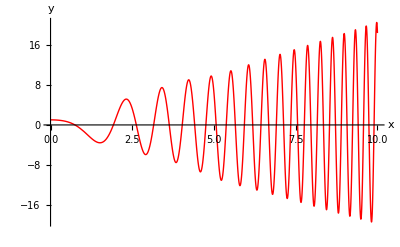

```mathematica
Plot[f'[√(t^2+1)], {t, 0, 10}, PlotStyle->{Red, Thick}, AxesLabel->{"x", "y"}]
```

```mathematica
(* cv 2 *)
rce=3*x^2+4*x+6==0;
vyraz=√x;
vys = Solve[rce, {x}][[2]];
vyraz /. vys
```

√(1/3 (-2+ⅈ √14))

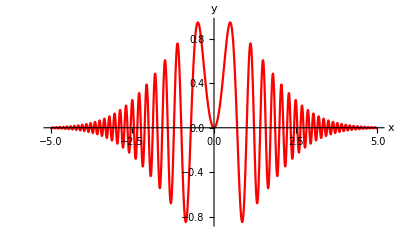

```mathematica
(* cv 3 *)
f[ω_,σ_,t_]:=Sin[ω*t] E^(-t^2/(2 σ^2));
Plot[f[2Pi * x, 1.5, x], {x, -5, 5}, AxesLabel-> {"x", "y"}, PlotStyle->{Red}]
```

```mathematica
(* cv 4 *)
```

```mathematica
uloha={-Subscript[x, 2]+3 Subscript[x, 1]==3,-6 Subscript[x, 1]+17 Subscript[x, 2]+2 Subscript[x, 3]==14,-21 Subscript[x, 1]+15 Subscript[x, 3]==3};
vyr=Subscript[x, 1]+Subscript[x, 2]-Subscript[x, 3];
vys = Solve[uloha, {Subscript[x, 1],Subscript[x, 2], Subscript[x, 3]}];
vyr /.vys
```

{75/239}